```mathematica
(2 E^(Iω (N-2-2 k+ q)) - E^(Iω (N-2 k+ q)) - E^(Iω (N-4-2 k+ q)))
2^(-N)(Binomial[N-2,(N+q)/2-1]2  - Binomial[N-2,(N+q)/2] -Binomial[N-2,(N+q)/2-2])
```

```mathematica
2^(-N)Binomial[N-2,(N+q)/2-1]FullSimplify[(2  - (Binomial[N-2,(N+q)/2] +Binomial[N-2,(N+q)/2-2])/Binomial[N-2,(N+q)/2-1])]
```

(2^(2-N) (N-q^2) Binomial[-2+N,-1+(N+q)/2])/(N^2-q^2)

```mathematica
(2^(2-N) (N-q^2) Binomial[N-2,(N+q)/2-1])/(N^2-q^2)
```

```mathematica
(2^(2-N) (N-q^2))/((N^2-q^2)N Beta[(N+q)/2+1,(N-q)/2+1]) FullSimplify[Binomial[-2+N,-1+(N+q)/2] N Beta[(N+q)/2+1,(N-q)/2+1]]
```

```mathematica
FullSimplify[(2^-N (N-q) (N+q) (N-q^2))/(N (-1+N^2) (N^2-q^2))] /Beta[1+(N+q)/2,1+(N-q)/2]
```

(2^-N (N-q^2))/(N (-1+N^2) Beta[1+(N+q)/2,1+(N-q)/2])

```mathematica
h[v_, N_] :=Log[1-v^2] - (3 +N )Log[2]- Log[Beta[1+(N+v Sqrt[N])/2,1+(N-v Sqrt[N])/2]]
```

```mathematica
FullSimplify[Exp[Series[FullSimplify[Normal[Series[h[v,N], {N , Infinity,2}]],{N > 1, 0 <v < 1}],{N,Infinity,2}]],{N >1, 0 < v < 1}]
```

-((ⅇ^(-v^2/2) (-1+v^2)) √N)/(4 √(2 π))+(ⅇ^(-v^2/2) (9-3 v^2-7 v^4+v^6) √(1/N))/(48 √(2 π))-((ⅇ^(-v^2/2) (-1+v^2) (-315+60 v^2+450 v^4-108 v^6+5 v^8)) (1/N)^(3/2))/(5760 √(2 π))+O[1/N]^2

```mathematica
UniqueFractions[L_] :=Select[Sort[Flatten[UniqueElements[TensorProduct[Range[L],1/Range[L]]]]],#<1&];
```

```mathematica
UniqueFractions[100];
```

```mathematica
ProbLog[L_, digits_]:=
Block[{fractions, Tau, taus, LW},
fractions = Select[Sort[Flatten[UniqueElements[TensorProduct[Range[L],1/Range[L]]]]],#<1&];
Tau[f_] :=With[{M= (L+1)^2,q = Denominator[f], p = Numerator[f]},
N[Log[(2^(-3-M) (M-q^2) Cot[(p π)/q]^2)/((1+M) Beta[1+(M+q)/2,1+(M-q)/2])],digits]];
taus =Sort[ ParallelTable[Tau[fractions[[i]]],{i, Length[fractions]}]];
LW=N[Log[1.-(#- 0.5)/Length[taus]],16] & /@Range[Length[taus]] ;
Transpose[{taus,LW}]
]
```

```mathematica
fitdata =ProbLog[500, 16];
```

```mathematica
lowdata = Select[fitdata, #[[1]] <1&];
lowmodel = LinearModelFit[lowdata,{x,x^2, x^3},x]
```

FittedModel[-0.30272-0.135185 x-0.0213599 x^2-0.0011033 x^3]

```mathematica
highdata = Select[fitdata, #[[1]] >2.5&];
highmodel = LinearModelFit[highdata,{x},x]
```

FittedModel[0.500467-0.503318 x]

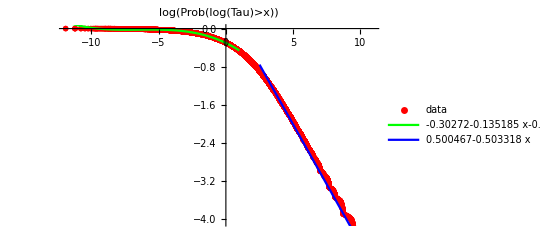

```mathematica
Show[
ListPlot[fitdata, PlotStyle->{Red, PointSize[0.01]},
PlotLegends->{"data"}],
Plot[lowmodel[x],{x,fitdata[[1]][[1]],1},PlotStyle->{Green, Thick},
PlotLegends->{Normal[lowmodel]},PlotRange->All],
Plot[highmodel[x],{x,2.5,fitdata[[-1]][[1]]},PlotStyle->{Blue, Thick},
PlotLegends->{Normal[highmodel]},PlotRange->All],
PlotLabel->Log[Prob[Log[Tau]> x ]]
]
```

```mathematica
Normal[lowmodel]
```

-0.30272-0.135185 x-0.0213599 x^2-0.0011033 x^3

```mathematica
Normal[highmodel]
```

0.500467-0.503318 x

```mathematica
lowmodel["ParameterTable"]
```

General::munfl: Exp[-27823.5] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-20168.8] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-13485.7] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.30272 | 0.0000943022 | -3210.11 | 0.
x | -0.135185 | 0.0001136 | -1190.01 | 0.
x^2 | -0.0213599 | 0.0000431513 | -494.999 | 0.
x^3 | -0.0011033 | 3.84113×10^-6 | -287.234 | 0.

```mathematica
highmodel["ParameterTable"]
```

General::munfl: Exp[-2816.04] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-13782.3] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.500467 | 0.0055966 | 89.4234 | 0.
x | -0.503318 | 0.00109004 | -461.743 | 0.

```mathematica
Integrate[E^( I ω q)Cos[ω]^(k-1)/(2 Pi),{ω,-Pi,Pi}, GenerateConditions->False]
```

$Aborted

```mathematica
(*z^q (1/2(z + 1/z))^(k-1) = z^(q + k-1) 2^(1-k)(1 + 1/z^2)^(k-1)= *)
z^(q + k-1- 2 l) 2^(1-k) Binomial[k-1,l]/.{l ->(q + k-1)/2, z->1}//FullSimplify
```

2^(1-k) Binomial[-1+k,1/2 (-1+k+q)]

```mathematica
2^(1-k)  Binomial[-1+k,1/2 (-1+k+q)]Theta[k-1 -1/2 (-1+k+q)]//Simplify
```

2^(1-k) Binomial[-1+k,1/2 (-1+k+q)] Theta[1/2 (-1+k-q)]

```mathematica
Sum[2^(1-k)  Binomial[-1+k,1/2 (-1+k+q)],{k ,n, m-1}]
```

2^(1-n) [m-n]

```mathematica
FullSimplify[Asymptotic[2^(1-k)  Binomial[-1+k,1/2 (-1+(k+q))],{q , Infinity,1},Assumptions->{0 < k < q,q >0}],{0 < k < q,q >0}]
```

(2 q^-k Cos[1/2 π (-k+q)] Gamma[k])/π

```mathematica
FullSimplify[Asymptotic[(1- k) Log[2] + LogGamma[k] - LogGamma[1/2 (1+q + k)] - LogGamma[1  -1+k- 1/2 (-1+(k+q))],{q, Infinity,2},Assumptions->{0 < k < q, q >0}],{0 < k < q, q >0}]
```

1/6 (-3 ⅈ k π+(k (-1+k^2))/q^2+3 ⅈ π q-6 Log[π]-6 k Log[q]+6 LogGamma[k])

```mathematica
F[x_] =(-ⅈ π (-1+x)-(-1+x) Log[1-x]+2 x Log[x]-(1+x) Log[1+x]);
```

```mathematica
D[F[x],x]//Simplify
```

-ⅈ π-Log[1-x]+2 Log[x]-Log[1+x]

```mathematica
Solve[-ⅈ π-Log[1-x]+2 Log[x]-Log[1+x]==0,x]
```

{}

```mathematica
Exp[q Normal[Series[F[x],{x,0,2}]]]//FullSimplify
```

ⅇ^(q (-ⅈ π (-1+x)-2 x+2 x Log[x]))

```mathematica
Sum[x^k,{k,n,m-1}]
```

(x^m-x^n)/(-1+x)

```mathematica
S[n_,m_] =Normal[Series[(Cos[β]^n - Cos[β]^m)/(2 Sin[β/2](m-n) (1-Cos[β])), {β,0,2}]]
```

1/β+1/24 (7-6 m-6 n) β

```mathematica
S[n,m] - S[m,n+N]//FullSimplify
```

(N β)/4

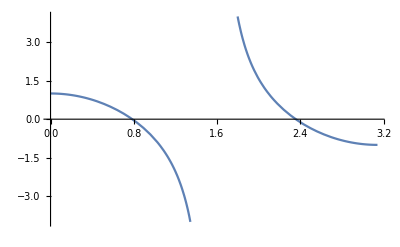

```mathematica
Plot[Cos[2 x]/Cos[x],{x,0,Pi}]
```

```mathematica
Simplify[TrigToExp[Sinh[Anm + I ω]Sinh[-Amn + I ω]]]//ExpToTrig//FullSimplify
```

-Sinh[Amn-ⅈ ω] Sinh[Anm+ⅈ ω]

```mathematica
(*(1/2(z + 1/z))^(N-2) ( X z  - 1/X 1/z)/2  (z/Y    - Y/z)/2 *)
```

```mathematica
TTT=Collect[2^(2-N) Binomial[N-2,k]z^(N - 2 k + q)( X z  - 1/X 1/z)/2  (z/Y    - Y/z)/2,z]
```

(2^-N Y z^(-2-2 k+N+q) Binomial[-2+N,k])/X+2^-N (-1/(X Y)-X Y) z^(-2 k+N+q) Binomial[-2+N,k]+(2^-N X z^(2-2 k+N+q) Binomial[-2+N,k])/Y

```mathematica
Sub =A_ z^(n_ -2 k):> (A/.k->n/2)
```

z^(-2 k+n_) A_:>(A/.k→n/2)

```mathematica
TTT/.Sub//FullSimplify
```

```mathematica
Binomial[-2+N,(N+q)/2]FullSimplify[((2^-N (Y^2 Binomial[-2+N,1/2 (-2+N+q)]/Binomial[-2+N,(N+q)/2]-(1+X^2 Y^2) +X^2 Binomial[-2+N,1/2 (2+N+q)]/Binomial[-2+N,(N+q)/2]))/(X Y))]
```

(2^-N (-1+((-4+N-q) X^2)/(2+N+q)+((N+q) Y^2)/(-2+N-q)-X^2 Y^2) Binomial[-2+N,(N+q)/2])/(X Y)

```mathematica
2^(-N)Binomial[-2+N,(N+q)/2]/(X Y)FullSimplify[(-1+((-4+N-q) X^2)/(2+N+q)+((N+q) Y^2)/(-2+N-q)-X^2 Y^2) ]
```

(2^-N (-1+((-4+N-q) X^2)/(2+N+q)+((N+q) Y^2)/(-2+N-q)-X^2 Y^2) Binomial[-2+N,(N+q)/2])/(X Y)

```mathematica
(* Euler *)
CorFunc=
Block[{α, Ads, Ap, Am, μp, μm , Sp, Sm, wp, wm},
 α ={0.814,0.887};
Ads = {3.84 10^(-4),2.09 10^(-4)};
Am = {45212.453,99532.825};
Ap = {33396.390,73284.727};
μm  = {1.257,1.340};
μp = {1.300,1.369};
Sp = {2446064,2252355};
Sm = {6551937,6747644};
wp = α/4 Ads Sp Ap/(Sp + Sm);
wm= α/4 Ads Sm Am/(Sp + Sm);
- wp ( 2 ν t/r^2)^((μp-α)/2)Cos[Pi ( α - μp)/2]Gamma[μp-α -1]
+ wm  (2 ν t/r^2)^((μm-α)/2)Cos[Pi ( α - μm)/2]Gamma[μm-α -1]
]
```

{-8.26396 ((t ν)/r^2)^0.2215+2.15109 ((t ν)/r^2)^0.243,-10.9529 ((t ν)/r^2)^0.2265+2.59023 ((t ν)/r^2)^0.241}

```mathematica
FullSimplify[Integrate[Exp[I ρ z (X-Y)Cos[β]]Sinh[ρ z X Sin[β] + I ω]Sinh[-ρ z Y Sin[β] + I ω],{z,-1,1}],{ρ>0,{ω,X,Y} ϵ Reals}]
```

1/(2 ρ)ⅇ^(-ⅈ (X-Y) ρ) ((ⅈ (-1+ⅇ^(2 ⅈ (X-Y) ρ)) (X-Y) Cosh[(X+Y) ρ Sin[β]])/((X-Y)^2+(X+Y)^2 Sin[β]^2)+(ⅇ^(ⅈ (X ρ-Y ρ-2 ω)) (ⅇ^(4 ⅈ ω) (1+ⅈ Sin[β]) Sin[(X-Y) ρ (1-ⅈ Sin[β])]+(1-ⅈ Sin[β]) Sin[(X-Y) ρ (1+ⅈ Sin[β])]))/((X-Y) (1+Sin[β]^2))-((1+ⅇ^(2 ⅈ (X-Y) ρ)) (X+Y) Sin[β] Sinh[(X+Y) ρ Sin[β]])/((X-Y)^2+(X+Y)^2 Sin[β]^2))

```mathematica
QQ =Integrate[Cos[ ρ z (X-Y)Cos[β]]/z^2(  - z^2ρ^2(X^2(N-q-4)/(N+ q + 2) + Y^2(N+ q)/(N-q-2)) + z^4 ρ^4 X^2 Y^2),{z,-1,1}, GenerateConditions->False]
```

1/((-2+N-q) (2+N+q) (X-Y)^3)ρ Sec[β] (4 (N^2-(2+q)^2) X^2 (X-Y) Y^2 ρ Cos[(X-Y) ρ Cos[β]] Sec[β]+2 ((X-Y)^2 (-((N^2+2 N (1+q)+q (2+q)) Y^2)+(-2+N-q) X^2 (4+q+2 Y^2 ρ^2+q Y^2 ρ^2+N (-1+Y^2 ρ^2)))-2 (N^2-(2+q)^2) X^2 Y^2 Sec[β]^2) Sin[(X-Y) ρ Cos[β]])

```mathematica
KK[a_, x_] =Integrate[Cos[ x z]/(z+I a)^2,{z,-1,1},  GenerateConditions->False]
```

-(2 Cos[x])/(1+a^2)-ⅈ x (CosIntegral[ⅈ (ⅈ+a) x]-CosIntegral[x+ⅈ a x]) Sinh[a x]-x Cosh[a x] (SinIntegral[x-ⅈ a x]+SinIntegral[x+ⅈ a x])

```mathematica
KK[0,ρ (X-Y)Cos[β]]
```

-2 Cos[(X-Y) ρ Cos[β]]-2 (X-Y) ρ Cos[β] SinIntegral[(X-Y) ρ Cos[β]]

```mathematica
FullSimplify[QQ + KK[0,ρ (X-Y)Cos[β]]]
```

```mathematica
-2 Cos[(X-Y) ρ Cos[β]]+(2 ρ Sec[β] Z)/(X-Y)^3+2 (-X+Y) ρ Cos[β] SinIntegral[(X-Y) ρ Cos[β]]
```

```mathematica
W = (X-Y)^2 (((4-N+q) X^2)/(2+N+q)+((N+q) Y^2)/(2-N+q)+X^2 Y^2 ρ^2)-2 X^2 Y^2 Sec[β]^2
```

```mathematica
Z = 2 X^2 (X-Y) Y^2 ρ Cos[(X-Y) ρ Cos[β]] Sec[β]+W Sin[(X-Y) ρ Cos[β]]
```

```mathematica
II = -2 Cos[(X-Y) ρ Cos[β]]+2 (-X+Y) ρ Cos[β] SinIntegral[(X-Y) ρ Cos[β]]+(2 ρ Sec[β] Z Sin[(X-Y) ρ Cos[β]])/(X-Y)^3
```